# Loading Initial Results

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
resX = 20; (* Incoming direction in [0,π/2[ *)
resY=10; (* Roughness in [0,1] *)
resZ=8;  (* Albedos in [0,1[ *)
rawFiles = Table[{i},{i,1,resZ}];
For[albedo=0,albedo<resZ,albedo++,{
str=OpenRead["results_order2_slice" <> ToString[albedo] <> ".bin",{BinaryFormat->True}];
rawFile = BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
rawFiles[[1+albedo]]= Table[Table[  rawFile[[1+resX*(j-1)+(i-1)]], {i,1,resX}],{j,1,resY}];
Close[str];
} ]
MatrixForm[rawFiles[[1]]];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse2\1) Fitting Scale\Export

# Parametrization of the Lobe’s Flattening Factor σ_n

```mathematica
paramsFlat = Table[Table[rawFiles[[albedo]][[j]][[i]][[4]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ ListPlot3D[paramsFlat[[1]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Red],
ListPlot3D[paramsFlat[[2]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Blue],
ListPlot3D[paramsFlat[[3]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Green],
ListPlot3D[paramsFlat[[4]],{ PlotRange->{0,1.2},AxesLabel->{"θ","α"}},PlotStyle->Yellow]
 ]
```

-Graphics3D-

We see that for most albedo values, the shape is very similar and there is no dependency on the albedo at all, which is good (only the global scale factor σ should be dependent on albedo).
We thus concentrate on albedo 1 to fit what seems to be a pretty straightforward shape, except when roughness becomes low in which case the fitter resorted to the default value and modified the other parameters instead.
So basically our range of confidence in α is from index 1 to about 9.
There is also a slight inflection of the curve for grazing angles indicating a slight dependency on θ.

### Representative Shape

First, we can notice the curve along θ seems to transform from a curve into a straight line when roughness decreases:

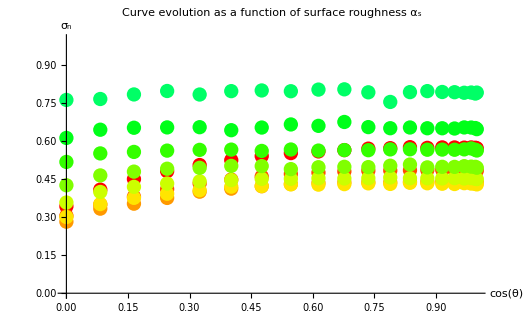

```mathematica
paramsFlat0=paramsFlat[[1]]; (* We only work on albedo = 1 *)
parmsFlatCurves= Table[Table[{Cos[(i-1)/(resX-1)*π/2],paramsFlat0[[j]][[i]]},{i,1,resX}],{j,1,9}];
Show[Table[ListPlot[parmsFlatCurves[[j]],PlotRange->{0,1},PlotStyle->Hue[(j-1)/(2*resY)],AxesLabel->{"cos(θ)","σ_n"},PlotLabel->"Curve evolution as a function of surface roughness α_s"],{j,1,9}]]
```

### Choosing the Model

```mathematica
Clear[a,b,c,d]
modelCurvature=a+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature},{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0.349241 | b→0.703137 | c→-0.750968 | d→0.273897
a→0.306658 | b→0.544117 | c→-0.546067 | d→0.180493
a→0.286569 | b→0.505814 | c→-0.557502 | d→0.205389
a→0.307424 | b→0.493074 | c→-0.643767 | d→0.276447
a→0.364296 | b→0.397045 | c→-0.564163 | d→0.256813
a→0.433438 | b→0.339749 | c→-0.536241 | d→0.264011
a→0.526302 | b→0.227204 | c→-0.390173 | d→0.205767
a→0.622109 | b→0.179252 | c→-0.257171 | d→0.106611
a→0.758224 | b→0.21125 | c→-0.35677 | d→0.17884)

Now let’s try and fit the individual parameters using another fitting for each one:

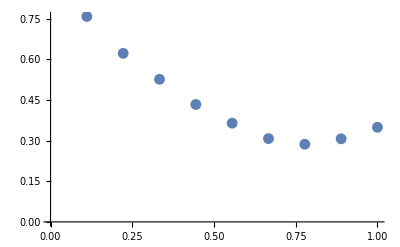

```mathematica
paramsFlatA=Table[{1-(j-1)/(resY-1), a/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatA]
ListPlot[paramsFlatB];
ListPlot[paramsFlatC];
ListPlot[paramsFlatD];
```

Parameter A is the most stable so let’s start with that one...

0.885056-1.21098 α+0.225698 α^2+0.449826 α^3

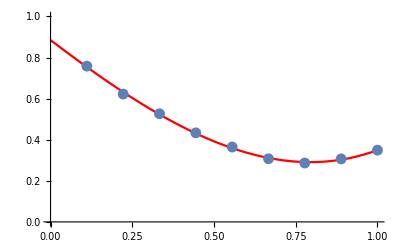

```mathematica
Clear[a,b,c,d]
modelA=a+b*u+c*u^2+d*u^3;
fittingA = FindFit[ paramsFlatA,{modelA},{a,b,c,d},u ];
fA[α_]=Evaluate[modelA/.fittingA/.u->α]
Show[Plot[fA[α],{α,0,1},PlotStyle->Red,PlotRange->{0,1}],
ListPlot[paramsFlatA]
]
```

#### Replacing A and Fitting Other Coefficients

Let’s now replace a by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0.700681 | c→-0.746451 | d→0.271447
a→0. | b→0.569665 | c→-0.593042 | d→0.205967
a→0. | b→0.4733 | c→-0.49772 | d→0.172969
a→0. | b→0.466591 | c→-0.595074 | d→0.250041
a→0. | b→0.43239 | c→-0.629149 | d→0.292055
a→0. | b→0.356837 | c→-0.56766 | d→0.28105
a→0. | b→0.248671 | c→-0.429644 | d→0.227173
a→0. | b→0.111985 | c→-0.133491 | d→0.0395393
a→0. | b→0.240522 | c→-0.41059 | d→0.208027)

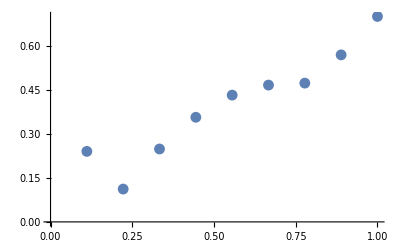

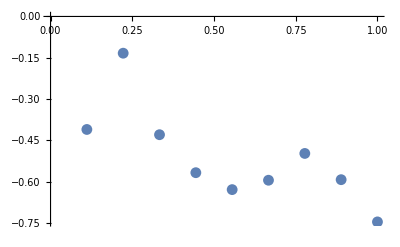

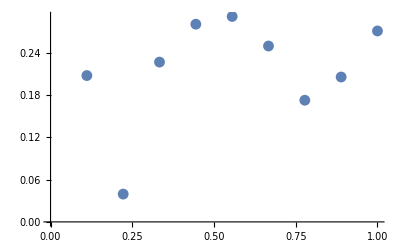

```mathematica
paramsFlatB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatB->{0,1}]
ListPlot[paramsFlatC->{-1,0}]
ListPlot[paramsFlatD->{0,1}]
```

We see the model is behaving a little bit better now so we can proceed and fit the next coefficients:

0.0856807+0.565903 α

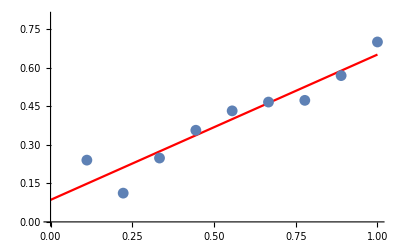

```mathematica
Clear[a,b,c,d]
modelB=a+b*u+0*c*u^2+0*d*u^3;
fittingB = FindFit[ paramsFlatB,{modelB},{a,b,c,d},u ];
fB[α_]=Evaluate[modelB/.fittingB/.u->α]
Show[Plot[fB[α],{α,0,1},PlotStyle->Red,PlotRange->{0,0.8}],
ListPlot[paramsFlatB]
]
```

#### Replacing B and Fitting Other Coefficients

Let’s now replace b by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature/.α->1-(j-1)/(resY-1)},{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-4.44089×10^-16 | c→-0.610497 | d→0.182801
a→0. | b→-7.77156×10^-16 | c→-0.645766 | d→0.240346
a→0. | b→-6.66134×10^-16 | c→-0.643174 | d→0.26781
a→0. | b→-5.55112×10^-16 | c→-0.58499 | d→0.243466
a→0. | b→-8.88178×10^-16 | c→-0.539657 | d→0.233703
a→0. | b→-5.55112×10^-16 | c→-0.513265 | d→0.245582
a→0. | b→-6.66134×10^-16 | c→-0.500654 | d→0.273474
a→0. | b→-4.44089×10^-16 | c→-0.408883 | d→0.219105
a→0. | b→-1.11022×10^-16 | c→-0.155935 | d→0.0419828)

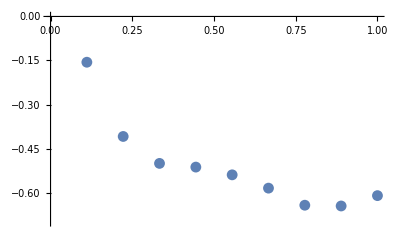

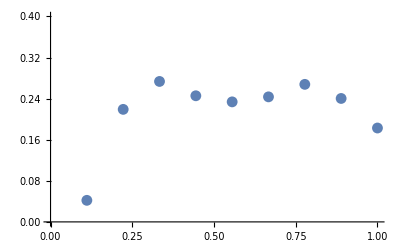

```mathematica
paramsFlatC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,9}];
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatC,PlotRange->{-0.7,0}]
ListPlot[paramsFlatD,PlotRange->{0,0.4}]
```

The model is continuing to improve in stability, let’s keep on replacing...

-0.0770746-1.38461 α+0.856589 α^2

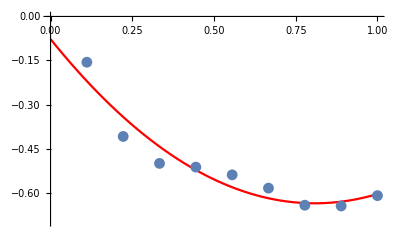

```mathematica
Clear[a,b,c,d]
modelC=a+b*u+c*u^2+0*d*u^3;
fittingC = FindFit[ paramsFlatC,{modelC},{a,b,c,d},u ];
fC[α_]=Evaluate[modelC/.fittingC/.u->α]
Show[Plot[fC[α],{α,0,1},PlotStyle->Red,PlotRange->{-0.7,0}],
ListPlot[paramsFlatC]
]
```

#### Replacing C and Fitting D

Let’s now replace c by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+fC[α]*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsFlatCurves[[j]],{modelCurvature/.α->1-(j-1)/(resY-1)},{a,b,c,d},u ],{j,1,9}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0. | c→0. | d→0.176974
a→0. | b→0. | c→0. | d→0.224436
a→0. | b→0. | c→0. | d→0.259863
a→0. | b→0. | c→0. | d→0.280669
a→0. | b→0. | c→0. | d→0.279344
a→0. | b→0. | c→0. | d→0.256371
a→0. | b→0. | c→0. | d→0.211691
a→0. | b→0. | c→0. | d→0.147389
a→0. | b→0. | c→0. | d→0.111532)

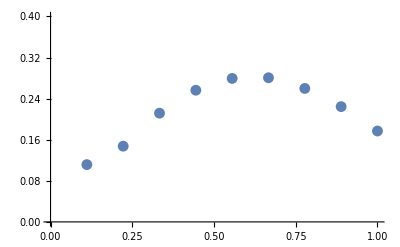

```mathematica
paramsFlatD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,9}];
ListPlot[paramsFlatD,PlotRange->{0,0.4}]
```

0.0104231+0.852559 α-0.684474 α^2

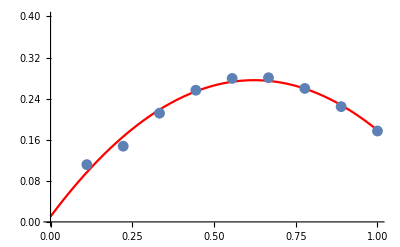

```mathematica
Clear[a,b,c,d]
modelD=a+b*u+c*u^2+0*d*u^3;
fittingD = FindFit[ paramsFlatD,{modelD},{a,b,c,d},u ];
fD[α_]=Evaluate[modelD/.fittingD/.u->α]
Show[Plot[fD[α],{α,0,1},PlotStyle->Red,PlotRange->{0,0.4}],
ListPlot[paramsFlatD]
]
```

Final Expression

So we end up with 4 coefficients a, b, c and d depending on surface roughness α_s to form an order 3 polynomial depending on μ = cos(θ) :

	a(α_s)= 0.885056-1.21098 α+0.225698 α^2+0.449826 α^3
	b(α_s)=0.0856807+0.565903 α
	c(α_s)= -0.0770746-1.38461 α+0.856589 α^2
	d(α_s)=0.0104231+0.852559 α-0.684474 α^2
	
	σ_n(μ,α_s) =a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3

```mathematica
Clear[a,b,c,d,σ,μ]
fA[α_]= 0.8850557867448499-1.2109761138443194 α+0.22569832413951335 α^2+0.4498256199595464 α^3;
fB[α_]= 0.0856807009397115+0.5659031384072539 α;
fC[α_]= -0.07707463071513312-1.384614678037336 α+0.8565888280926491 α^2;
fD[α_]=0.010423083821992304+0.8525591060832015 α-0.6844738691665317 α^2;

fFlat[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;
fFlat[0.99691733373312797619777340874204,0.3333]

Plot[fA[σ],{σ,0,1}];
Plot[fB[σ],{σ,0,1}];
Plot[fC[σ],{σ,0,1}];
Plot[fD[σ],{σ,0,1}];
Plot3D[fFlat[μ,σ],{μ,0,1},{σ,0,1},AxesLabel->{"cos(θ)","α_s""σ_n"},PlotLabel->"Lobe flattening factor",PlotRange->{0,1}]
```

0.572465

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsFlat0,PlotRange->{0,1},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[fFlat[Cos[(i-1)/(resX-1)π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Pretty good! 
Now we can remove that parameter from the simulation and use our fitting instead. That should help us stabilize the other parameters...

# Parametrization of the lobe’s Scale factor σ

## IMPORTANT! => I forgot a factor 2 at the denominator of the Phong normalization factor which I took as (n+2)/π instead of (n+2)/(2π)so we need to assume a scale parameter effectively DOUBLE of what was fitted!

```mathematica
(*paramsScale = Table[Table[rawFiles[[albedo]][[j]][[i]][[3]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];*)

(* Assume DOUBLE scale value *)
paramsScale = Table[Table[  2 *  rawFiles[[albedo]][[j]][[i]][[3]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
```

```mathematica
Show[ 
Table[ListPlot3D[paramsScale[[albedo]],{ PlotRange->{0,2.4},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->GrayLevel[1-(albedo-1)/resZ]],{albedo,1,resZ}]
]
```

-Graphics3D-

So it appears the scale factor σ is also quite smooth and should be fitted in the same way as the flattening factor σ_n.

### Representative Shape

First, we can notice the curve along θ seems to transform from a curve into a straight line when roughness decreases:

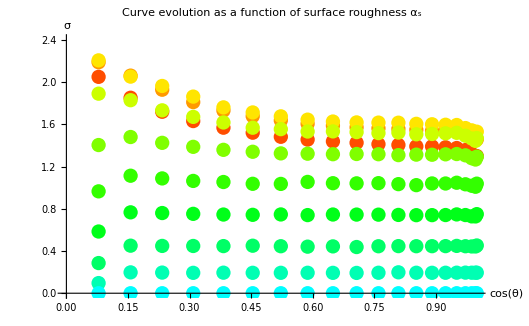

```mathematica
paramsScale0=paramsScale[[1]]; (* We only work on albedo = 1 *)
parmsScaleCurves= Table[Table[{Cos[(i-1)/resX*π/2],paramsScale0[[j]][[i]]},{i,1,resX}],{j,1,resY}];
Show[Table[ListPlot[parmsScaleCurves[[j]],PlotRange->{0,2.4},PlotStyle->Hue[j/(2*resY)],AxesLabel->{"cos(θ)","σ"},PlotLabel->"Curve evolution as a function of surface roughness α_s"],{j,1,resY}]]
```

### Choosing the Model

```mathematica
Clear[a,b,c,d]
modelCurvature=a+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],{modelCurvature},{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→2.2695 | b→-3.23848 | c→4.41454 | d→-2.13075
a→2.42021 | b→-2.96025 | c→3.6877 | d→-1.67138
a→2.41624 | b→-2.78436 | c→3.44283 | d→-1.53104
a→2.04457 | b→-1.86959 | c→2.35415 | d→-1.05486
a→1.47389 | b→-0.340095 | c→0.171985 | d→-0.00970127
a→0.980927 | b→0.566536 | c→-1.11803 | d→0.605011
a→0.5643 | b→1.11714 | c→-1.94381 | d→1.00916
a→0.25471 | b→1.14749 | c→-1.99082 | d→1.04437
a→0.0796 | b→0.674402 | c→-1.15255 | d→0.598335
a→2.×10^-6 | b→7.76979×10^-23 | c→-1.87721×10^-21 | d→-6.60779×10^-22)

Now let’s try and fit the individual parameters using another fitting for each one:

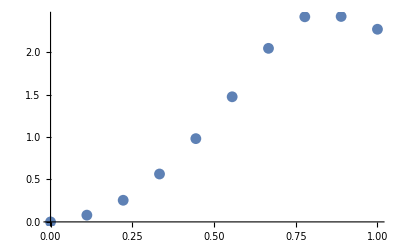

```mathematica
paramsScaleA=Table[{1-(j-1)/(resY-1), a/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleA]
ListPlot[paramsScaleB];
ListPlot[paramsScaleC];
ListPlot[paramsScaleD];
```

All curves seem to behave the same way so let’s simply start with coefficient a:

0.0576265-1.84307 α+13.2655 α^2-9.1914 α^3

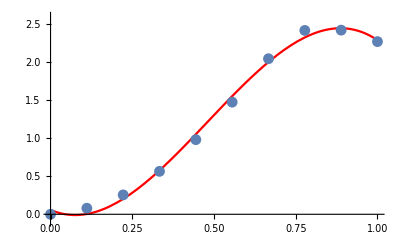

```mathematica
Clear[a,b,c,d]
modelA=a+b*u+c*u^2+d*u^3;
fittingA = FindFit[ paramsScaleA,{modelA},{a,b,c,d},u ];
fA[α_]=Evaluate[modelA/.fittingA/.u->α]
Show[Plot[fA[α],{α,0,1},PlotStyle->Red,PlotRange->{-0.1,2.6}],
ListPlot[paramsScaleA]
]
```

#### Replacing A and Fitting Other Coefficients

Let’s now replace a by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+b*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-3.36822 | c→4.65336 | d→-2.26035
a→0. | b→-3.13042 | c→4.00093 | d→-1.84136
a→0. | b→-2.15973 | c→2.2931 | d→-0.907075
a→0. | b→-1.57557 | c→1.81295 | d→-0.76115
a→0. | b→-0.87026 | c→1.14784 | d→-0.539299
a→0. | b→0.0845059 | c→-0.230781 | d→0.123496
a→0. | b→1.03234 | c→-1.78771 | d→0.92444
a→0. | b→1.50367 | c→-2.64644 | d→1.40017
a→0. | b→1.1879 | c→-2.09772 | d→1.11128
a→0. | b→-0.391419 | c→0.720469 | d→-0.391)

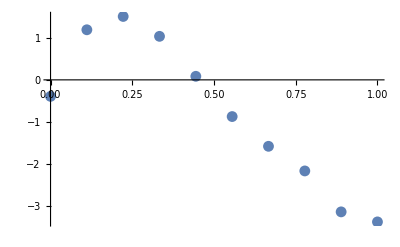

```mathematica
paramsScaleB=Table[{1-(j-1)/(resY-1),b/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleB]
ListPlot[paramsScaleC];
ListPlot[paramsScaleD];
```

-0.193265+14.4283 α-39.5737 α^2+22.0841 α^3

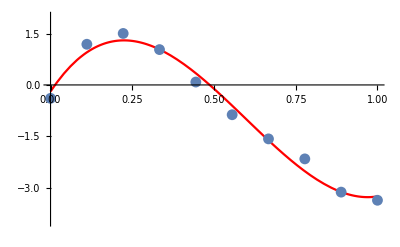

```mathematica
Clear[a,b,c,d]
modelB=a+b*u+c*u^2+d*u^3;
fittingB = FindFit[ paramsScaleB,{modelB},{a,b,c,d},u ];
fB[α_]=Evaluate[modelB/.fittingB/.u->α]
Show[Plot[fB[α],{α,0,1},PlotStyle->Red,PlotRange->{-4,2}],
ListPlot[paramsScaleB]
]
```

#### Replacing B and Fitting Other Coefficients

Let’s now replace b by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+c*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→-5.32907×10^-15 | c→4.33852 | d→-2.05502
a→0. | b→-3.55271×10^-15 | c→3.98824 | d→-1.83309
a→0. | b→-2.66454×10^-15 | c→3.29138 | d→-1.55813
a→0. | b→-1.33227×10^-15 | c→1.934 | d→-0.840096
a→0. | b→-3.33067×10^-16 | c→0.412973 | d→-0.060035
a→0. | b→8.88178×10^-16 | c→-0.941414 | d→0.586957
a→0. | b→1.77636×10^-15 | c→-1.80068 | d→0.932897
a→0. | b→1.77636×10^-15 | c→-2.08541 | d→1.03428
a→0. | b→1.33227×10^-15 | c→-1.44326 | d→0.684459
a→0. | b→-1.11022×10^-16 | c→0.171642 | d→-0.0330661)

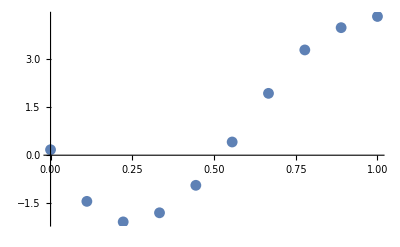

```mathematica
paramsScaleC=Table[{1-(j-1)/(resY-1),c/.fittingCurvatures[[j]]},{j,1,resY}];
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleC]
ListPlot[paramsScaleD];
```

0.218714-21.5808 α+57.0161 α^2-31.3305 α^3

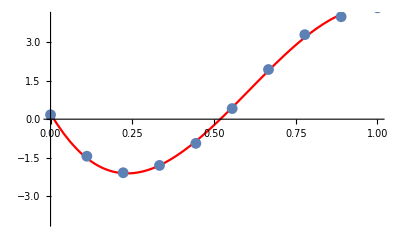

```mathematica
Clear[a,b,c,d]
modelC=a+b*u+c*u^2+d*u^3;
fittingC = FindFit[ paramsScaleC,{modelC},{a,b,c,d},u ];
fC[α_]=Evaluate[modelC/.fittingC/.u->α]
Show[Plot[fC[α],{α,0,1},PlotStyle->Red,PlotRange->{-4,4}],
ListPlot[paramsScaleC]
]
```

#### Replacing C and Fitting the D Coefficient

Let’s now replace c by its analytical expression and fit the new model again:

```mathematica
Clear[a,b,c,d]
modelCurvature=fA[α]+fB[α]*u+fC[α]*u^2+d*u^3;
fittingCurvatures = Table[FindFit[ parmsScaleCurves[[j]],modelCurvature/.α->1-(j-1)/(resY-1),{a,b,c,d},u ],{j,1,resY}];
MatrixForm[fittingCurvatures]
```

(a→0. | b→0. | c→0. | d→-2.03876
a→0. | b→0. | c→0. | d→-1.93337
a→0. | b→0. | c→0. | d→-1.44172
a→0. | b→0. | c→0. | d→-0.791347
a→0. | b→0. | c→0. | d→-0.105163
a→0. | b→0. | c→0. | d→0.499968
a→0. | b→0. | c→0. | d→0.932334
a→0. | b→0. | c→0. | d→1.05569
a→0. | b→0. | c→0. | d→0.765428
a→0. | b→0. | c→0. | d→-0.0839083)

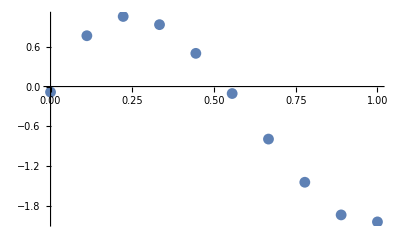

```mathematica
paramsScaleD=Table[{1-(j-1)/(resY-1),d/.fittingCurvatures[[j]]},{j,1,resY}];
ListPlot[paramsScaleD]
```

-0.0875285+10.4984 α-27.1654 α^2+14.6968 α^3

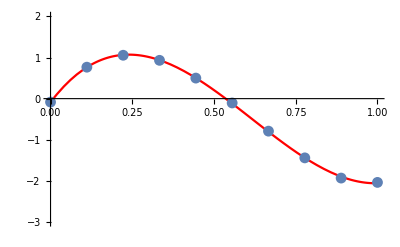

```mathematica
Clear[a,b,c,d]
modelD=a+b*u+c*u^2+d*u^3;
fittingD = FindFit[ paramsScaleD,{modelD},{a,b,c,d},u ];
fD[α_]=Evaluate[modelD/.fittingD/.u->α]
Show[Plot[fD[α],{α,0,1},PlotStyle->Red,PlotRange->{-3.0,2}],
ListPlot[paramsScaleD]
]
```

Final Expression

So we end up with 4 coefficients a, b, c and d depending on surface roughness α_s to form an order 3 polynomial depending on μ = cos(θ) :

	a(α_s)= 0.0576265-1.84307 α+13.2655 α^2-9.1914 α^3
	b(α_s)= -0.193265+14.4283 α-39.5737 α^2+22.0841 α^3
	c(α_s)= 0.218714-21.5808 α+57.0161 α^2-31.3305 α^3
	d(α_s)=-0.0875285+10.4984 α-27.1654 α^2+14.6968 α^3
	
	σ(μ,σ_s) =a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3

```mathematica
Clear[a,b,c,d,σ,μ,fA,fB,fC,fD]
fA[α_]=0.057626522306966195-1.8430749623241764 α+13.265452228771144 α^2-9.1914044613068 α^3
fB[α_]= -0.19326518084394056+14.428287204401842 α-39.57369023420125 α^2+22.084117767595018 α^3
fC[α_]= 0.21871385093630663-21.580810315041887 α+57.01607335273474 α^2-31.33051654652553 α^3
fD[α_]=-0.08752850960291476+10.498392018375801 α-27.165414679434377 α^2+14.696817709205297 α^3

fScale[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;
Plot[fA[α],{α,0,1}];
Plot[fB[α],{α,0,1}];
Plot[fC[α],{α,0,1}];
Plot[fD[α],{α,0,1}];
Plot3D[fScale[μ,α],{μ,0,1},{α,0,1},AxesLabel->{"cos(θ)","α_s""α"},PlotLabel->"Lobe Scale factor",PlotRange->{0,2.5}]
```

(0.218714-21.5808 α+57.0161 α^2-31.3305 α^3) (0.0576265-1.84307 α+13.2655 α^2-9.1914 α^3) (-0.0875285+10.4984 α-27.1654 α^2+14.6968 α^3) (-0.193265+14.4283 α-39.5737 α^2+22.0841 α^3)

-Graphics3D-

```mathematica
fScale[Cos[π/4],1.0]
fFlat[Cos[π/4],1.0]
```

0.710748

0.570905

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsScale0,PlotRange->{0,2.4},AxesLabel->{"θ","α"},PlotStyle->Blue],
Plot3D[fScale[Cos[(i-1)/resX π/2],1-(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Great!
Now we only need to find the dependence between the scale and the albedo...

# Dependence of Scale σ on albedo ρ

We try to fit our scale model to all albedo using the “amp” free coefficient to see how the amplitude is related to ρ:

```mathematica
paramsScaleMuAlpha = Table[
	Table[
		{ Cos[Mod[i,resX]/resX*π/2], 1-Quotient[i,resX]/(resY-1),paramsScale[[albedo]][[1+Quotient[i,resX]]][[1+Mod[i,resX]]]},{i,0,resX*resY-1}]
, {albedo,1,resZ}];
paramsScaleMuAlpha[[1]];
ListPlot3D[paramsScaleMuAlpha[[1]]];
```

{{amp→1.},{amp→0.769408},{amp→0.565958},{amp→0.395722},{amp→0.260114},{amp→0.21669},{amp→0.155062},{amp→0.00676621}}

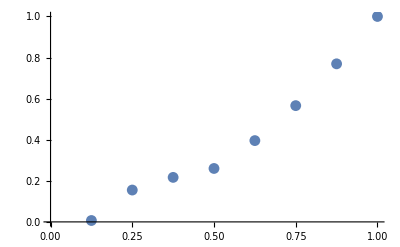

```mathematica
modelRho=amp * fScale[μ,α];
fittingRho = Table[FindFit[ paramsScaleMuAlpha[[albedo]],{modelRho},{amp},{μ,α} ],{albedo,1,resZ}]
listAmps=Table[{1-(albedo-1)/resZ, amp/.fittingRho[[albedo]]},{albedo,1,resZ}];
ListPlot[listAmps,PlotRange->{0,1.0}]
```

{a→0.,b→0.175378,c→0.804716}

0.175378 ρ+0.804716 ρ^2

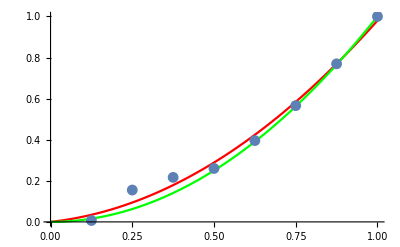

```mathematica
modelAmp=0*a+b*u+c*u^2;
fittingAmp=FindFit[listAmps,modelAmp,{a,b,c},u]
fAmp[ρ_]=Evaluate[modelAmp/.fittingAmp/.u->ρ]
fAmp2[ρ_]=ρ^2;
Show[
Plot[fAmp[ρ],{ρ,0,1},PlotStyle->Red,PlotRange->{0,1}],
Plot[fAmp2[ρ],{ρ,0,1},PlotStyle->Green,PlotRange->{0,1}],
ListPlot[listAmps]
]
```

Final Expression

We obtain the final expression for the scale parameter σ :

	a(α_s)= 0.0288133-0.921537 α+6.63273 α^2-4.5957 α^3
	b(α_s)= -0.0966326+7.21414 α-19.7868 α^2+11.0421 α^3
	c(α_s)= 0.109357-10.7904 α+28.508 α^2-15.6653 α^3
	d(α_s)=-0.0437643+5.2492 α-13.5827 α^2+7.34841 α^3

	σ(μ,σ_s, ρ) = ρ^2 [ a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3]

```mathematica
fScale2[μ_,α_,ρ_] = ρ^2 * fScale[μ,α];
```

```mathematica
Show[ 
Table[ListPlot3D[paramsScaleMuAlpha[[albedo]],{ PlotRange->{0,2.5},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->GrayLevel[1-(albedo-1)/resZ]],{albedo,1,6}],
Table[Plot3D[fScale2[μ,α,1-(albedo-1)/resZ],{μ,0,1},{α,0,1},{ PlotRange->{0,2.5},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->Red],{albedo,1,6}]
]
```

-Graphics3D-

And we’re done with a very good match for scale!